```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
a=Import["species_A.txt","Table"];
b=Import["species_B.txt","Table"];c=Import["species_C.txt","Table"];
```

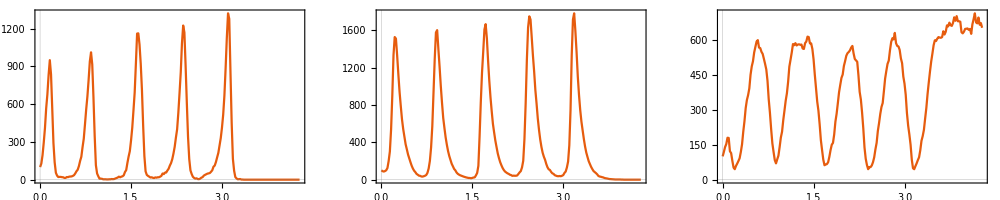

```mathematica
GraphicsRow[{
ListLinePlot[a],
ListLinePlot[b],
ListLinePlot[c]
},ImageSize->1000]
```

```mathematica
dat=Transpose[{a[[;;,2]],b[[;;,2]],c[[;;,2]]}];
Show[ListPointPlot3D@dat,Graphics3D@Line@dat]
```

-Graphics3D-